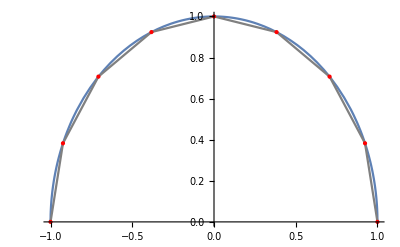

```mathematica
DivisionPointsG= {};
For [i = 0,i ≤ 8,i++,
DivisionPointsG = Insert[DivisionPointsG,N[CoordinateTransform["Polar"-> "Cartesian",{1, i/8 π}],10],-1]
]
Show[Plot[Sqrt[1-x^2],{x,-1,1}], ListLinePlot[DivisionPointsG,PlotStyle->{PointSize[Large],Gray}],ListPlot[DivisionPointsG,PlotStyle->{PointSize[Large],Red}]]
```

```mathematica
NumberDivideG= 60;
TotalNumberPointsG=2*NumberDivideG;
```

```mathematica
PointsOnCurveG = {};
For[i=0,i≤ 2*NumberDivideG,i++,
PointsOnCurveG = Insert[PointsOnCurveG,i/(2*NumberDivideG),-1]
];
PointsXG=N[Cos[PointsOnCurveG*π],10];
PointsYG=N[Sin[PointsOnCurveG*π],10];
SegmentsLenG = {};
For[i=1,i≤ TotalNumberPointsG,i++,
SegmentsLenG=Insert[SegmentsLenG,Norm[N[{PointsXG[[i+1]]-PointsXG[[i]],PointsYG[[i+1]]-PointsYG[[i]]}]],-1]
];
NormalPointsXG ={};
For[i=1,i≤ TotalNumberPointsG,i++,
NormalPointsXG = Insert[NormalPointsXG,(PointsYG[[i+1]]-PointsYG[[i]])/SegmentsLenG[[i]],-1]
];
NormalPointsYG ={};
For[i=1,i≤ TotalNumberPointsG,i++,
NormalPointsYG = Insert[NormalPointsYG,-(PointsXG[[i+1]]-PointsXG[[i]])/SegmentsLenG[[i]],-1]
];
FG=Function[{i,k,x,y},
FA=Function[kk,SegmentsLenG[[kk]]^2][k];
FB=Function[{kk,xx,yy},(-NormalPointsYG[[kk]]*(PointsXG[[kk]]-xx)+NormalPointsXG[[kk]]*(PointsYG[[kk]]-yy))*2*SegmentsLenG[[kk]]][k,x,y];
FE=Function[{kk,xx,yy},(PointsXG[[kk]]-xx)^2+(PointsYG[[kk]]-yy)^2][k,x,y];
Decision=4*FA*FE-FB^2;
If[i == 1,
Re[If[Decision==0,SegmentsLenG[[k]]/(2*π)*(Log[SegmentsLenG[[k]]]+(1+FB/(2*FA))*Log[Abs[1+FB/(2*FA)]]-FB/(2*FA)*Log[Abs[FB/(2*FA)]]-1),
SegmentsLenG[[k]]/(4*π)*(2*(Log[SegmentsLenG[[k]]]-1)-FB/(2*FA)*Log[Abs[FE/FA]]+(1+FB/(2*FA))*Log[Abs[1+(FB+FE)/FA]]+Sqrt[Decision]/FA*(ArcTan[(2*FA+FB)/Sqrt[Decision ]]-ArcTan[FB/Sqrt[Decision ]]))
]]
,Re[If[Decision ==0,0,SegmentsLenG[[k]]*((NormalPointsXG[[k]]*(PointsXG[[k]]-x)+NormalPointsYG[[k]]*(PointsYG[[k]]-y))/(π*Sqrt[Decision ]))*(ArcTan[(2*FA+FB)/Sqrt[Decision ]]-ArcTan[FB/Sqrt[Decision ]])
]]
]
];
```

```mathematica
MidPointsXG=N[Cos[(PointsOnCurveG+1/(TotalNumberPointsG*2))*π]];
MidPointsYG=N[Sin[(PointsOnCurveG+1/(TotalNumberPointsG*2))*π]];
BoundsG={};
For[i=1,i≤ TotalNumberPointsG,i++,
BoundsG = Insert[BoundsG,1,-1];
];
FactorXG= {};
For[i=1,i≤ TotalNumberPointsG,i++,
FactorXG = Insert[FactorXG,(PointsXG[[i+1]]-PointsXG[[i]])/2+PointsXG[[i]],-1];
]; 
FactorYG= {};
For[i=1,i≤ TotalNumberPointsG,i++,
FactorYG = Insert[FactorYG,(PointsYG[[i+1]]-PointsYG[[i]])/2+PointsYG[[i]],-1];
]; 
aG = {};
For[i=1,i≤ TotalNumberPointsG,i++,
Temp = {};
For[j=1,j≤ TotalNumberPointsG,j++,
Temp = Insert[Temp,N[-(FG[1,j,FactorXG[[i]],FactorYG[[i]]]-FG[1,j,FactorXG[[i]],-FactorYG[[i]]])],-1];
];
aG = Insert[aG,Temp,-1];
];
bG = {};
For[i=1,i≤ TotalNumberPointsG,i++,
Temp = {};
For[j=1,j≤ TotalNumberPointsG,j++,
Temp = Insert[Temp,N[BoundsG[[j]]*(-FG[2,j,FactorXG[[i]],FactorYG[[i]]]+FG[2,j,FactorXG[[i]],-FactorYG[[i]]]+Function[{ii,jj},If[ii== jj,1,0]][i,j]/2)],-1];
];
bG = Insert[bG,Sum[Temp[[k]],{k,1,TotalNumberPointsG}],-1];
];
zG=LinearSolve[aG, bG];
BoundsUG = {};
For[i=1,i≤ TotalNumberPointsG,i++,
BoundsUG = Insert[BoundsUG,N[BoundsG[[i]]],-1];
];
BoundsNG = {};
For[i=1,i≤ TotalNumberPointsG,i++,
BoundsNG = Insert[BoundsNG,zG[[i]],-1];
];
```

```mathematica
BEMG=Function[{x,y},Sum[BoundsUG[[i]]*(FG[2,i,x,y]-FG[2,i,x,-y])-BoundsNG[[i]]*(FG[1,i,x,y]-FG[1,i,x,-y]) ,{i,1,TotalNumberPointsG}]];
```

```mathematica
Plot3D[BEMG[x,y],{x,-1,1},{y,0,Sqrt[1-x^2]}]
```

$Aborted